# Similarity Index of 1D Cellular Automata

## Inheritance properties in CA increasing definitions

Erick Jesse Angeles Lopez

### Hypergraph of transitions

## ECA with inheritance rules

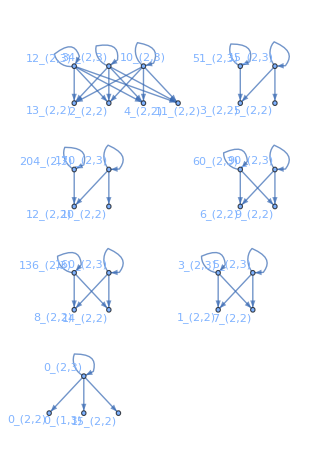
```mathematica
Grid[{{-Graphics-,and   74 unclassified behaviors: {Subscript[1, 2,3],Subscript[2, 2,3],Subscript[4, 2,3],Subscript[6, 2,3],Subscript[7, 2,3],Subscript[8, 2,3],Subscript[9, 2,3],Subscript[11, 2,3],Subscript[13, 2,3],Subscript[14, 2,3],Subscript[18, 2,3],Subscript[19, 2,3],Subscript[22, 2,3],Subscript[23, 2,3],Subscript[24, 2,3],Subscript[25, 2,3],Subscript[26, 2,3],Subscript[27, 2,3],Subscript[28, 2,3],Subscript[29, 2,3],Subscript[30, 2,3],Subscript[32, 2,3],Subscript[33, 2,3],Subscript[35, 2,3],Subscript[36, 2,3],Subscript[37, 2,3],Subscript[38, 2,3],Subscript[40, 2,3],Subscript[41, 2,3],Subscript[42, 2,3],Subscript[43, 2,3],Subscript[44, 2,3],Subscript[45, 2,3],Subscript[46, 2,3],Subscript[50, 2,3],Subscript[54, 2,3],Subscript[56, 2,3],Subscript[57, 2,3],Subscript[58, 2,3],Subscript[62, 2,3],Subscript[72, 2,3],Subscript[73, 2,3],Subscript[74, 2,3],Subscript[76, 2,3],Subscript[77, 2,3],Subscript[78, 2,3],Subscript[94, 2,3],Subscript[104, 2,3],Subscript[105, 2,3],Subscript[106, 2,3],Subscript[108, 2,3],Subscript[110, 2,3],Subscript[122, 2,3],Subscript[126, 2,3],Subscript[128, 2,3],Subscript[130, 2,3],Subscript[132, 2,3],Subscript[134, 2,3],Subscript[138, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[146, 2,3],Subscript[150, 2,3],Subscript[152, 2,3],Subscript[154, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[164, 2,3],Subscript[168, 2,3],Subscript[172, 2,3],Subscript[178, 2,3],Subscript[184, 2,3],Subscript[200, 2,3],Subscript[232, 2,3]}}},Alignment->Top]
```

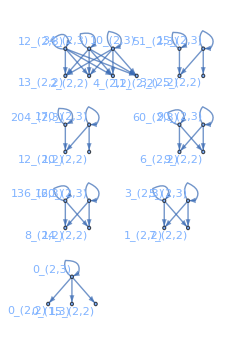
-Graphics- | and   74 unclassified behaviors: {1_(2,3),2_(2,3),4_(2,3),6_(2,3),7_(2,3),8_(2,3),9_(2,3),11_(2,3),13_(2,3),14_(2,3),18_(2,3),19_(2,3),22_(2,3),23_(2,3),24_(2,3),25_(2,3),26_(2,3),27_(2,3),28_(2,3),29_(2,3),30_(2,3),32_(2,3),33_(2,3),35_(2,3),36_(2,3),37_(2,3),38_(2,3),40_(2,3),41_(2,3),42_(2,3),43_(2,3),44_(2,3),45_(2,3),46_(2,3),50_(2,3),54_(2,3),56_(2,3),57_(2,3),58_(2,3),62_(2,3),72_(2,3),73_(2,3),74_(2,3),76_(2,3),77_(2,3),78_(2,3),94_(2,3),104_(2,3),105_(2,3),106_(2,3),108_(2,3),110_(2,3),122_(2,3),126_(2,3),128_(2,3),130_(2,3),132_(2,3),134_(2,3),138_(2,3),140_(2,3),142_(2,3),146_(2,3),150_(2,3),152_(2,3),154_(2,3),156_(2,3),162_(2,3),164_(2,3),168_(2,3),172_(2,3),178_(2,3),184_(2,3),200_(2,3),232_(2,3)}

### Rules < |states|

The behavior of the rules less than the number of states has always the same periodic evolution.

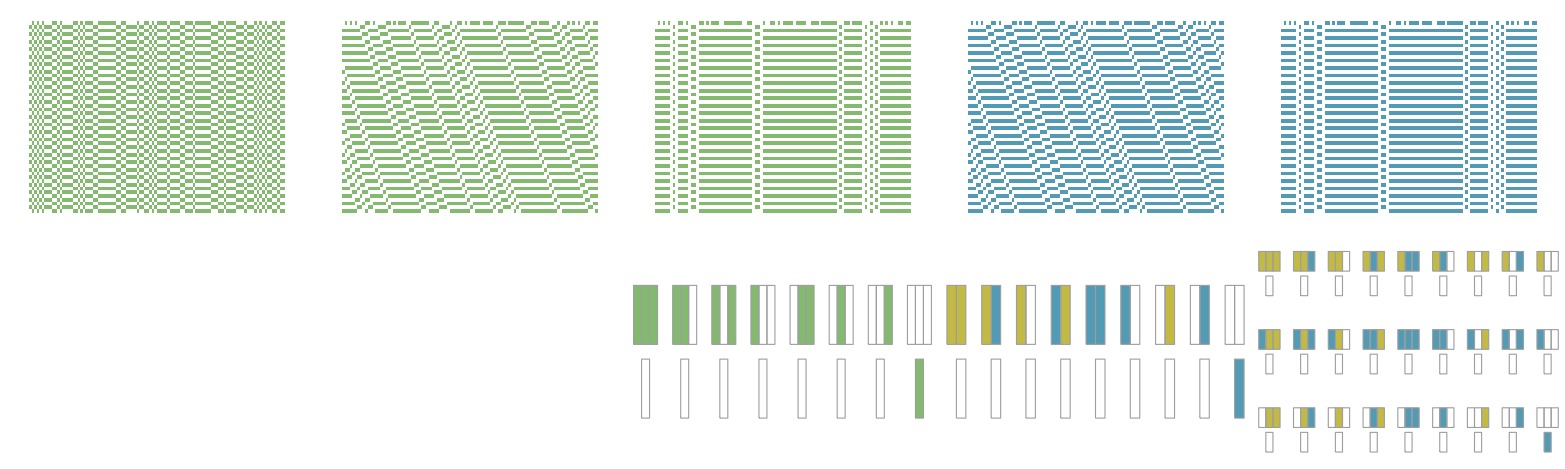

Evolution of rule  in 256 conditions   -Graphics-

### Rules that evolve to 0

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8_(2,3) | 32_(2,3) | 40_(2,3) | 128_(2,3) | 168_(2,3)

0_(2,3) | 8_(2,3) | 32_(2,3) | 40_(2,3) | 128_(2,3) | 136_(2,3) | 160_(2,3) | 168_(2,3)
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Proportion of ones and zeros

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],ColorRules->colorRules[ca[[2]]-1],opts];
rules=;
onePoints=;
Manipulate[Grid[{{rules[[h]],ListLinePlot[onePoints[rules[[h]]],PlotRange->{{0,9},{0,1}},Mesh->Full,ImageSize->Medium,LabelingFunction->Above],CaRulePlot[rules[[h]],ImageSize->Small]}}],{h,1,Length[rules],1}]
```

# Thanks